# Lab 3: Functions Assignment

### Instructions

Welcome to the assignment for Lab 3. The purpose of this assignment is to assess your ability to use functions in Mathematica. Some things to remember as you complete this assignment:
1. Save the notebook to your computer right away, and save your work often. 
2. When you have finished all the exercises, close any unnecessary cells and save as a PDF.
3. Upload the PDF on Canvas.
4. Do not delete this notebook. Save all your work until after the semester is over and your final grade has been issued.

### Question 1 Defining a function.

a) Define a function of two variables to be  f(x,y)=y^3-3^x

```mathematica
f[x_,y_]=y^3-3^x;
```

b) Evaluate your function at the point (1,-3).

```mathematica
f[1,-3]
```

-30

### Question 2 Working with multiple functions.

a) Define a new function to be “a sin(b x)”, where a, b, and x are the inputs in your function.

```mathematica
f2[a_,b_,x_]=a Sin[b x];
```

b) To confirm that you have defined your function correctly, plot your function leaving x as a variable and using the value of 2 for both a and b (i.e functionname[x,2,2]). The result should be a plot of the sine curve.

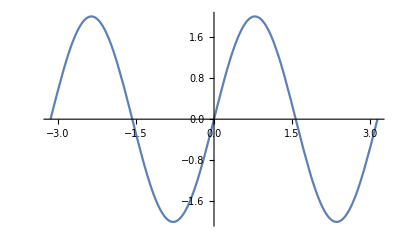

```mathematica
Plot[f2[2,2,x],{x,-π,π}]
```

c) Create a manipulate that displays the plot of your function with sliders to control the parameters “a” and “b”. You may need to refer to the document center to see the format for using Manipulate with two parameters. Note, you will need to use the PlotRange command to better see the effects of changing “a”.

```mathematica
Manipulate[Plot[f2[a,b,x],{x,-π,π},PlotRange->{{-π,π},{-5,5}}],{{a,0},-5,5},{{b,0},-10,10}]
```

d) In a text cell, describe the effect of changing each of the parameters “a” and “b”.

“a” changes the amplitude of the sin function while “b” changes the frequency of the sin function.

### Question 3 Calculus

a) Define a new function “g” to be 4 x^2+1.

```mathematica
g[x_]=4 x^2+1;
```

b) Plot the function along with its first two derivatives on the same plot from x=-3 to x=3.

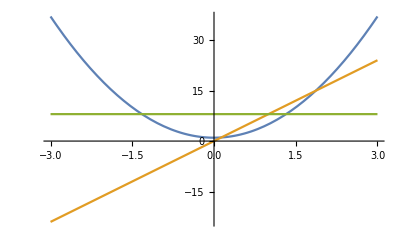

```mathematica
Plot[{g[x],g'[x],g''[x]},{x,-3,3}]
```